# ROM: Domača naloga 1

Učni list - Deljivost.pdf: 14. naloga: Izračunaj največji skupni deljitelj in najmanjši skupni večkratnik števil:

a) 176, 308

```mathematica
GCD[176, 308]
```

44

```mathematica
LCM[176, 308]
```

1232

b) 112, 294

```mathematica
GCD[112,294]
```

14

```mathematica
LCM[112,294]
```

2352

c) 189, 324

```mathematica
GCD[189,324]
```

27

```mathematica
LCM[189,324]
```

2268

d) 117, 273

```mathematica
GCD[117,273]
```

39

```mathematica
LCM[117,273]
```

819

Učni list - Računanje z izrazi.pdf: 1. naloga: Izračunaj vrednost veččlenika oziroma polinoma pri dani vrednosti neznanke:

a) p(x) = x^2 - 5x - 6

```mathematica
p = x^2 - 5x - 6
p/. x-> 3
```

-6-5 x+x^2

-12

b) p(x) = 3 x^2 - 4x + 5

```mathematica
ClearAll[p, x]
p = 3 x^2 - 4x + 5
p/. x -> -2
```

5-4 x+3 x^2

25

c) p(x) = x^3 - 5 x^2 + 2x - 4

```mathematica
ClearAll[p, x]
p = x^3 - 5 x^2 + 2x - 4
p/. x -> 1
```

-4+2 x-5 x^2+x^3

-6

d) p(x) =  5 x^3 + 11 x^2 - 46

```mathematica
ClearAll[p, x]
p = 5 x^3 + 11 x^2 - 46
p/. x -> -3
```

-46+11 x^2+5 x^3

-82

e) p(x) =  2 x^3 + 3 x^2 - 9x - 7

```mathematica
ClearAll[p, x]
p = 2 x^3 + 3 x^2 - 9x - 7
p/. x -> 4
```

-7-9 x+3 x^2+2 x^3

133

f) p(x) =  x^4 + 4 x^3 -6x  + 2

```mathematica
ClearAll[p, x]
p = x^4 + 4 x^3 -6x  + 2
p/. x -> -1
```

2-6 x+4 x^3+x^4

5

Učni list - Linearna funkcija.pdf: 4. naloga: Določi enačbo linearne funkcije, ki ima:
a) smerni koeficient (0,6)^2 in gre skozi točko A(10, 2).
b) začetno vrednost (0,2)^-1 in gre skozi točko B(3, 7).
c) smerni koeficient (1 1/2)^-2 in gre skozi točko C(6, -1).

```mathematica
Solve[10*(0.6)^2+ n == 2, n]
```

{{n→-1.6}}

Enačba premice a) je y = 0,36x - 1,6.

```mathematica
Solve[3k  + (0.2)^-1 == 7, k]
```

{{k→0.666667}}

Enačba premice b) je y = 2/3x + 5.

```mathematica
Solve[6*(3/2)^-2+ n == -1, n]
```

{{n→-11/3}}

Enačba premice c) je y = 4/9x - 11/3.

Učni list - Računanje s koreni.pdf: 4. naloga: Kvadriraj:

a) (4 + √2)^2
b) (3 - √5)^2
c) (5 + 2 √3)^2 
d) (2 - 3 √6)^2
e) (√5 + 8)^2 
f) (√2 + √7)^2

```mathematica
NSolve[(4 + √2)^2 == x, x]
```

{{x→29.3137}}

```mathematica
NSolve[(3 - √5)^2 == x, x]
```

{{x→0.583592}}

```mathematica
NSolve[(5 + 2 √3)^2 == x, x]
```

{{x→71.641}}

```mathematica
Simplify[(5 + 2 √3)^2]
```

37+20 √3

```mathematica
NSolve[(2 - 3 √6)^2 == x, x]
```

{{x→28.6061}}

```mathematica
Simplify[(2 - 3 √6)^2]
```

58-12 √6

```mathematica
NSolve[(√5 + 8)^2 == x, x]
```

{{x→104.777}}

```mathematica
Simplify[(√5 + 8)^2 ]
```

(8+√5)^2

```mathematica
NSolve[(√2 + √7)^2 == x, x]
```

{{x→16.4833}}

```mathematica
Simplify[(√2 + √7)^2]
```

9+2 √14

Učni list - Potence z racionalnimi eksponenti.pdf: 6. naloga: Reši enačbo:

a) (6x- 1)^8 == 6561
b) ((6x + 11)/5 - 3)^7 == 16384
c) ((3x - 1)/2 + 4)^5 == 16807
d) ((8x + 2)/5 + 7)^6 == 15625

```mathematica
Solve[(6x- 1)^8 == 6561, x]
```

{{x→-1/3},{x→1/6-ⅈ/2},{x→1/6+ⅈ/2},{x→2/3},{x→(-1/12+ⅈ/12) ((-1-ⅈ)+3 √2)},{x→(-1/12-ⅈ/12) ((-1+ⅈ)+3 √2)},{x→(1/12+ⅈ/12) ((1-ⅈ)+3 √2)},{x→(1/12-ⅈ/12) ((1+ⅈ)+3 √2)}}

```mathematica
Solve[((6x + 11)/5 - 3)^7 == 16384, x]
```

{{x→4},{x→Root[833344+208224 #1+52560 #1^2+11880 #1^3+4860 #1^4-486 #1^5+729 #1^6&,1]},{x→Root[833344+208224 #1+52560 #1^2+11880 #1^3+4860 #1^4-486 #1^5+729 #1^6&,2]},{x→Root[833344+208224 #1+52560 #1^2+11880 #1^3+4860 #1^4-486 #1^5+729 #1^6&,3]},{x→Root[833344+208224 #1+52560 #1^2+11880 #1^3+4860 #1^4-486 #1^5+729 #1^6&,4]},{x→Root[833344+208224 #1+52560 #1^2+11880 #1^3+4860 #1^4-486 #1^5+729 #1^6&,5]},{x→Root[833344+208224 #1+52560 #1^2+11880 #1^3+4860 #1^4-486 #1^5+729 #1^6&,6]}}

```mathematica
Solve[((3x - 1)/2 + 4)^5 == 16807, x]
```

{{x→7/3},{x→7/6 (-3-√5-ⅈ √(2 (5-√5)))},{x→7/6 (-3-√5+ⅈ √(2 (5-√5)))},{x→7/6 (-3+√5-ⅈ √(2 (5+√5)))},{x→7/6 (-3+√5+ⅈ √(2 (5+√5)))}}

```mathematica
Solve[((8x + 2)/5 + 7)^6 == 15625, x]
```

{{x→-31/4},{x→-3/2},{x→1/16 (-99-25 ⅈ √3)},{x→1/16 (-49-25 ⅈ √3)},{x→1/16 (-99+25 ⅈ √3)},{x→1/16 (-49+25 ⅈ √3)}}

Učni list - Kvadratna funkcija.pdf: 4. naloga: Za kateri x ima funcija f(x) = 2 x^2- 20x + 62  najmanjšo vrednost? Kolikšna je ta vrednost?

```mathematica
f[x_] := 2 x^2- 20x + 62
```

```mathematica
FindMinValue[2 x^2- 20x + 62, x]
```

12.

Funkcija ima najmanjšo vrednost pri x = 12.

```mathematica
2 * 12^2- 20* 12 + 62
```

110

Za vrednost x = 12 ima funkcija f(x) vrednost 110.

Učni list - Logaritem - 1.pdf: 4. naloga: Z uporabo definicije logaritma reši naslednje logaritemske enačbe:
	a)  log_3(x) = 2
	b)  log_10(x) = -2
	c)  log_9(x) = 2/3
	d)  (log(x))_9 = -3/2
	(e)  log(x))_125 = 1/3
	(f)  log(x))_(1/5) = -3

```mathematica
Solve[3^2 == x, x]
```

{{x→9}}

```mathematica
Solve[10^-2== x, x]
```

{{x→1/100}}

```mathematica
Solve[9^(2/3) == x, x]
```

{{x→3 3^(1/3)}}

```mathematica
Solve[9^(-3/2) == x, x]
```

{{x→1/27}}

```mathematica
Solve[125^(1/3) == x, x]
```

{{x→5}}

```mathematica
Solve[(1/5)^-3  == x, x]
```

{{x→125}}

Učni list - Polinomi - 1.pdf: 13. naloga: Poišči vse ničle polinoma:

a) p(x) = 3 x^3 - 5 x^2 - 4x + 20
b) p(x) = x^3 - 8 x^2 + 11x + 20
c) p(x) = x^3 - x^2 - x + 1
d) p(x) = x^4 - 6 x^3 +3 x^2 + 26x - 24
e) p(x) = 25 x^4 - 105 x^3 +118 x^2 - 12x - 8
f) p(x) = x^4 + 2 x^3 - 3 x^2 - 4x  + 4

```mathematica
Solve[3 x^3 - 5 x^2 - 4x + 20 == 0, x]
```

{{x→1/9 (5-61/(2035-18 √12081)^(1/3)-(2035-18 √12081)^(1/3))},{x→5/9+(61 (1+ⅈ √3))/(18 (2035-18 √12081)^(1/3))+1/18 (1-ⅈ √3) (2035-18 √12081)^(1/3)},{x→5/9+(61 (1-ⅈ √3))/(18 (2035-18 √12081)^(1/3))+1/18 (1+ⅈ √3) (2035-18 √12081)^(1/3)}}

```mathematica
Solve[x^3 - 8 x^2 + 11x + 20 == 0, x]
```

{{x→-1},{x→4},{x→5}}

```mathematica
Solve[x^3 - x^2 - x + 1 == 0, x]
```

{{x→-1},{x→1},{x→1}}

```mathematica
Solve[x^4 - 6 x^3 +3 x^2 + 26x - 24 == 0, x]
```

{{x→-2},{x→1},{x→3},{x→4}}

```mathematica
Solve[25 x^4 - 105 x^3 +118 x^2 - 12x - 8 == 0, x]
```

{{x→-1/5},{x→2/5},{x→2},{x→2}}

```mathematica
Solve[x^4 + 2 x^3 - 3 x^2 - 4x  + 4 == 0, x]
```

{{x→-2},{x→-2},{x→1},{x→1}}

Učni list - Racionalna funkcija-1.pdf: 5. naloga: Nariši graf racionalne funkcije:

a) f(x) = (x - 2)/(x+ 4)

```mathematica
f[x_]:= (x - 2)/(x + 4)
nicle = Solve[f[x] == 0, x]
```

{{x→2}}

```mathematica
poli = Solve[Denominator[f[x] ] == 0, x]
```

{{x→-4}}

```mathematica
Limit[f[x], x->-4, Direction->-1]
```

-∞

```mathematica
Limit[f[x], x -> Infinity]
```

1

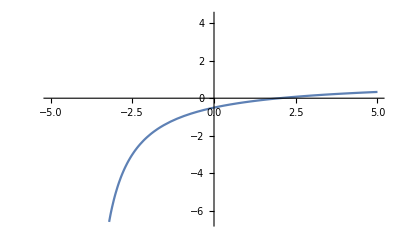

```mathematica
Plot[f[x], {x, -5, 5}]
```

b) f(x) = (3x + 7)/(-x+ 2)

```mathematica
ClearAll[f, x]
f[x_]:= (3x + 7)/(-x + 2)
```

```mathematica
nicle = Solve[{f[x] == 0} , x ]
```

{{x→-7/3}}

```mathematica
poli = Solve[Denominator[f[x] ] == 0, x]
```

{{x→2}}

```mathematica
Limit[f[x], x->2, Direction->+1]
```

∞

```mathematica
Limit[f[x], x -> -Infinity]
```

-3

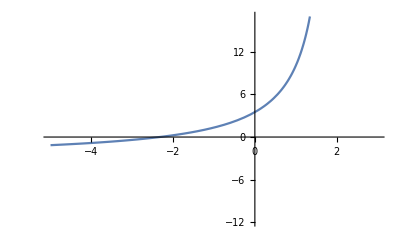

```mathematica
Plot[f[x], {x, -5, 3}]
```

c) f(x) = x/(x + 1)

```mathematica
ClearAll[f, x]
f[x_]:= x/(x + 1)
```

```mathematica
nicle = Solve[{f[x] == 0} , x ]
```

{{x→0}}

```mathematica
poli = Solve[Denominator[f[x] ] == 0, x]
```

{{x→-1}}

```mathematica
Limit[f[x], x->-1, Direction->-1]
```

-∞

```mathematica
Limit[f[x], x -> Infinity]
```

1

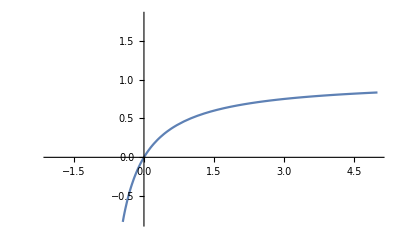

```mathematica
Plot[f[x], {x, -2, 5}]
```

d) f(x) = (-2x - 5)/x

```mathematica
ClearAll[f, x]
f[x_]:= (-2x - 5)/x
```

```mathematica
nicle = Solve[{f[x] == 0} , x ]
```

{{x→-5/2}}

```mathematica
poli = Solve[Denominator[f[x] ] == 0, x]
```

{{x→0}}

```mathematica
Limit[f[x], x->0, Direction->+1]
```

∞

```mathematica
Limit[f[x], x -> -Infinity]
```

-2

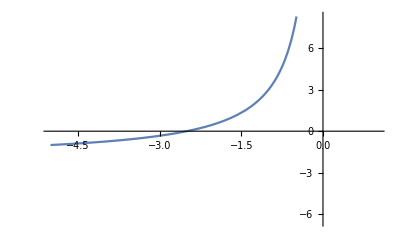

```mathematica
Plot[f[x], {x, -5, 1}]
```

Učni list - Integral.pdf: 2. naloga: Integriraj:

```mathematica
Integrate[(x^4+ 2 x^3 - 5x)/x^2, x]
```

x^2+x^3/3-5 Log[x]

```mathematica
Integrate[(x^4 - x^3  + 2x)/x^4, x]
```

-1/x^2+x-Log[x]

```mathematica
Integrate[(2 x^4 - x^3 - x)/x^3, x]
```

1/x-x+x^2

```mathematica
Integrate[(x^5- 4 x^2 + 2)/x^3, x]
```

-1/x^2+x^3/3-4 Log[x]

```mathematica
Integrate[(2 x^5+ x^3 - x^2)/x^4, x]
```

1/x+x^2+Log[x]

```mathematica
Integrate[(28 x^5- 12 x^4 - 5x)/x^2, x]
```

-4 x^3+7 x^4-5 Log[x]